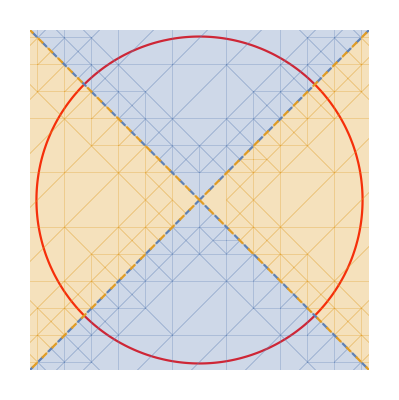

```mathematica
p1=ParametricPlot[{Sin[kx],Cos[kx]},{kx,-Pi,Pi},PlotStyle->Directive[Red],Axes->False];
p3=RegionPlot[{Cos[kx]-Cos[ky]>0,Cos[kx]-Cos[ky]<0},{kx,-Pi,Pi},{ky,-Pi,Pi},BoundaryStyle->Dashed];
Show[{p1,p3}]
```

```mathematica
Ham[kx_,ky_]:=Module[{tx=1.0,ty=1.0,del=0.5},{{tx Cos[kx]+ty Cos[ky],0,del(Cos[kx]-Cos[ky]),0},{0,tx Cos[kx]+ty Cos[ky],0,del(Cos[kx]-Cos[ky])},{del(Cos[kx]-Cos[ky]),0,-(tx Cos[kx]+ty Cos[ky]),0},{0,del(Cos[kx]-Cos[ky]),0,-(tx Cos[kx]+ty Cos[ky])}}]
```

```mathematica
val=DeleteDuplicates@Eigenvalues@Ham[kx,ky];
Plot3D[val,{kx,-Pi,Pi},{ky,-Pi,Pi},ImageSize->Large,PlotTheme->"Scientific",BoxRatios->{1, 1, 1},AxesStyle->Directive[Red, 32]]
```

-Graphics3D-